```mathematica
<<PlotLegends`
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
tab = Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{n,lam},{n,0,10}]
Γscatt = tab[[All, 2]]
```

Set::write: Tag Times in 1\ 485760. is Protected.

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,73641.1},{2,134305.},{3,184914.},{4,228076.},{5,265660.},{6,299075.},{7,329418.},{8,357589.},{9,384275.},{10,410188.}}

{0,73641.1,134305.,184914.,228076.,265660.,299075.,329418.,357589.,384275.,410188.}

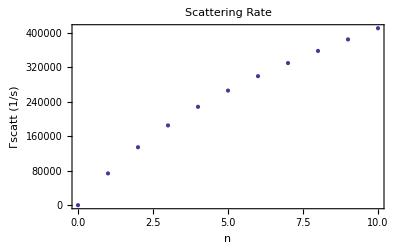

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

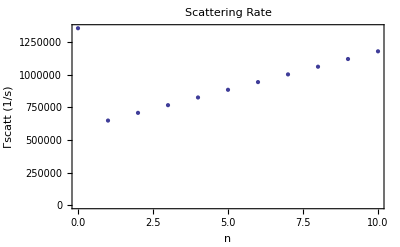

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
Scattering Rate As a Function of Raman and Repump Coupling strengths.
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{ΩR,lam},{ΩR,0,4 10^6, 2 10^4}],{n,1,10}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0538473.

Set::write: Tag Times in 0\ 485760. is Protected.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0329955.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0516823.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

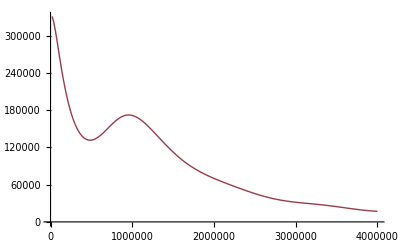
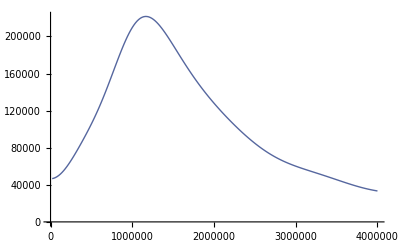
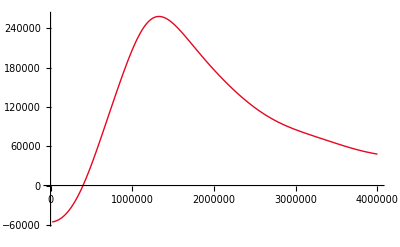
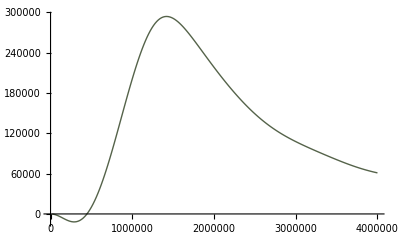
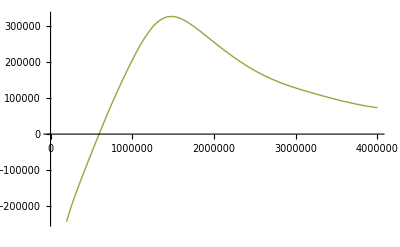
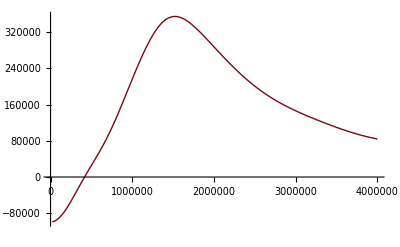
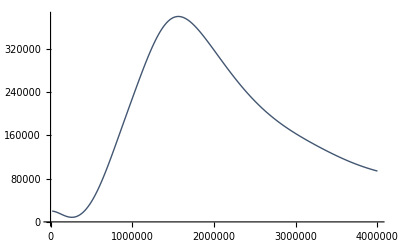
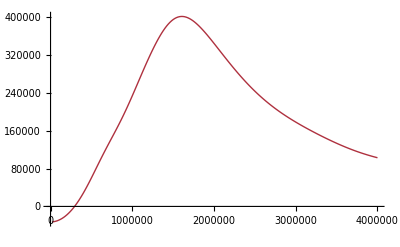

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

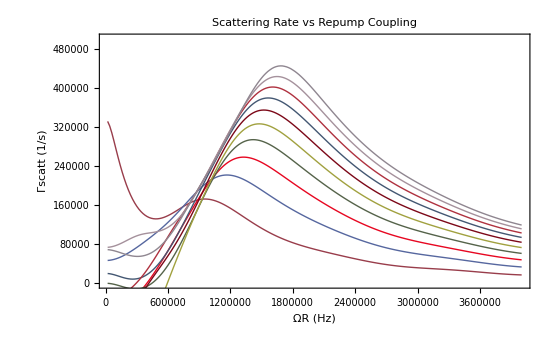

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,1,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

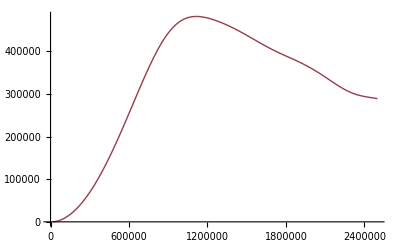
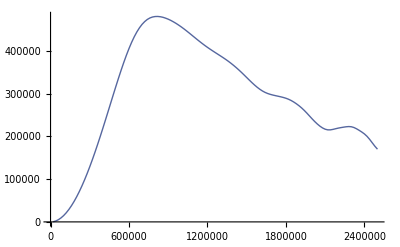
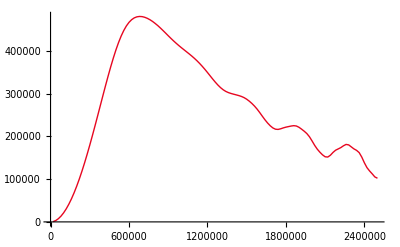
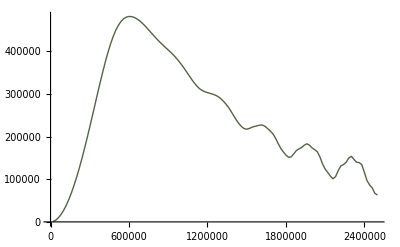
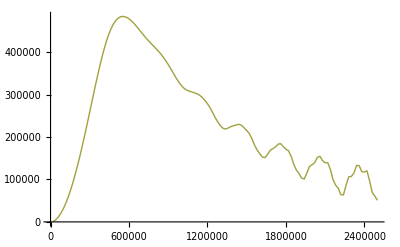
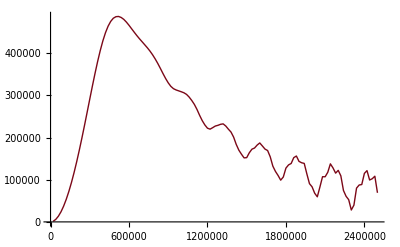
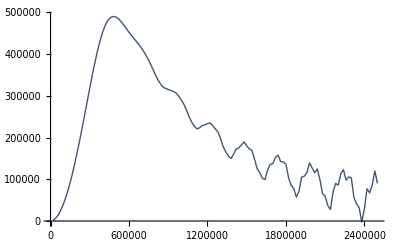
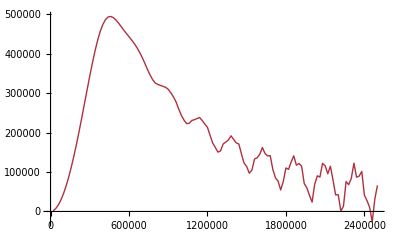

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

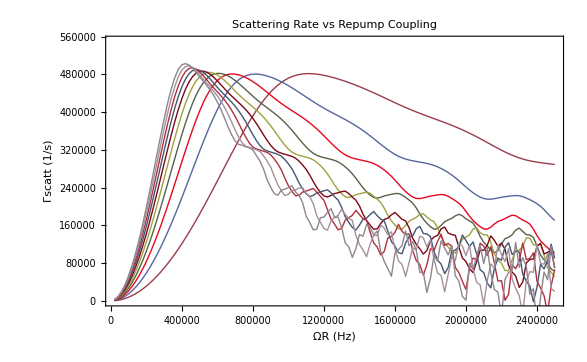

```mathematica
Show[ramanplots , PlotRange -> {All,{0,550000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
Photon recoil
```

```mathematica
Γscatt
```

{0,73641.1,134305.,184914.,228076.,265660.,299075.,329418.,357589.,384275.,410188.}

```mathematica
pphoton = h / λ
```

1.45459×10^-27

```mathematica
mCs = 132.90545 * 1.660539 10^-27
```

2.20695×10^-25

```mathematica
Erecoil = pphoton^2/(2mCs)
```

4.7936×10^-30

```mathematica
kb = 1.38066 10^-23;
```

```mathematica
Λrec= Γscatt * Erecoil
```

{0.,3.53006×10^-25,6.43807×10^-25,8.86404×10^-25,1.0933×10^-24,1.27347×10^-24,1.43364×10^-24,1.5791×10^-24,1.71414×10^-24,1.84206×10^-24,1.96628×10^-24}

```mathematica
ΛrecRate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,17.0453,31.0869,42.801,52.7914,61.4908,69.2251,76.2485,82.769,88.946,94.9439}